## Rutinas

```mathematica
(*Matriz de 1s por encima de la diagonal*)
I1[n_]:=SparseArray[Table[{i,i+1},{i,n-1}]->ConstantArray[1,n-1],{n,n}]
```

```mathematica
(*Matriz de 1s por debajo de la diagonal*)
Im1[n_]:=Transpose[I1[n]]
```

```mathematica
(*Matriz sparse de la identidad*)
Id[n_]:=SparseArray[IdentityMatrix[n]]
```

```mathematica
(*Potencial*)
V[x_,a_]:=x^2+x^4+a x
```

## Probando cómo funcionan las rutinas

```mathematica
I1[5]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

```mathematica
Im1[5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0)

```mathematica
Id[5]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Manipulate[Plot[V[x,a],{x,-1,1}],{a,-1,1}]
```

```mathematica
FindMinimum[V[t,-0.1],{t,-1}]
```

{-0.00249381,{t→0.0497537}}

## El problema

```mathematica
(*Cantidad de puntos*)
n=201;
```

```mathematica
(*Puntos inicial y final*)
x0=-5;xf=5;
```

```mathematica
(*Espaciado*)
d=N[(xf-x0)/(n-1)]
```

0.05

```mathematica
(*Valores de a*)
a=-1;
```

```mathematica
(*Valores de x*)
x=Table[x0+d*h,{h,0,n-1}];
```

```mathematica
(*Matriz A*)
A=N[(Im1[n]-2Id[n]+I1[n])/d^2];
```

```mathematica
(*Matriz B*)
B=N[(Im1[n]+10.Id[n]+I1[n])/12.]
```

SparseArray[…]

```mathematica
InvB=Chop[Inverse[B]];
```

```mathematica
NumerovK=0.5InvB.A;
```

```mathematica
(*Operador de potencial*)
Voperator=SparseArray[DiagonalMatrix[V[x,a]]]
```

SparseArray[…]

```mathematica
(*Calcular el espectro*)
{eigE,eigStates}=Reverse/@Chop[Eigensystem[-NumerovK+Voperator]];
eigStates=eigStates/Sqrt[d];
```

```mathematica
points=Table[Transpose[Append[{x},eigStates[[i]]]],{i,1,1}];
```

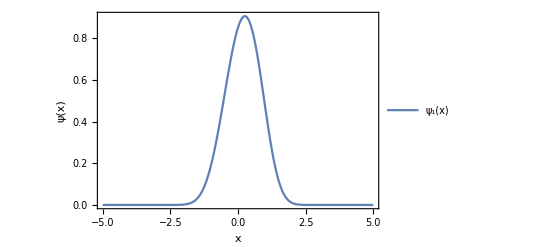

```mathematica
ListPlot[points,PlotRange->All,Joined->True,FrameStyle->Directive[FontWeight->"Plain",Black,13],Frame->True,FrameLabel->{"x","ψ(x)"},PlotLegends->{"ψ_1(x)","ψ_1(x)","ψ_1(x)","ψ_4(x)","ψ_5(x)"}]
```

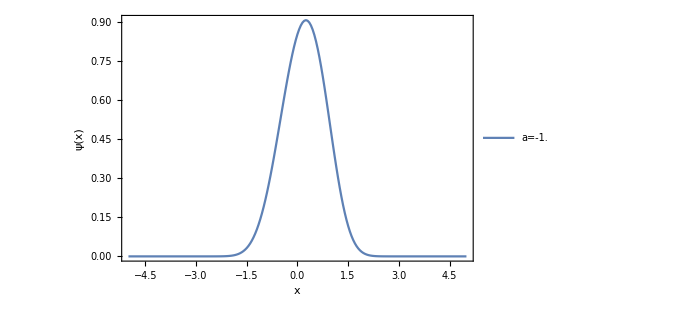

```mathematica
points=Table[Numerov[V,-5,5,a,200],{a,-1,-1,0.2}];
legendLabels=Table["a="<>ToString[a],{a,-1,-1,0.2}];

ListPlot[points,PlotRange->All,Joined->True,FrameStyle->Directive[FontWeight->"Plain",Black,13],Frame->True,FrameLabel->{"x","ψ(x)"},PlotLegends->legendLabels,ImageSize->500]
```

```mathematica
points
```

{{{-5.,0.},{-4.95,0.},{-4.9,0.},{-4.85,0.},{-4.8,0.},{-4.75,0.},{-4.7,0.},{-4.65,0.},{-4.6,0.},{-4.55,0.},{-4.5,0.},{-4.45,0.},{-4.4,0.},{-4.35,0.},{-4.3,0.},{-4.25,0.},{-4.2,0.},{-4.15,0.},{-4.1,0.},{-4.05,0.},{-4.,0.},{-3.95,0.},{-3.9,0.},{-3.85,0.},{-3.8,0.},{-3.75,0.},{-3.7,0.},{-3.65,0.},{-3.6,0.},{-3.55,0.},{-3.5,0.},{-3.45,0.},{-3.4,0.},{-3.35,0.},{-3.3,7.68693×10^-10},{-3.25,1.73722×10^-9},{-3.2,3.83748×10^-9},{-3.15,8.28869×10^-9},{-3.1,1.75119×10^-8},{-3.05,3.62031×10^-8},{-3.,7.32626×10^-8},{-2.95,1.45178×10^-7},{-2.9,2.81809×10^-7},{-2.85,5.36049×10^-7},{-2.8,9.99555×10^-7},{-2.75,1.82775×10^-6},{-2.7,3.27862×10^-6},{-2.65,5.77145×10^-6},{-2.6,9.97368×10^-6},{-2.55,0.0000169261},{-2.5,0.0000282192},{-2.45,0.0000462354},{-2.4,0.0000744733},{-2.35,0.000117972},{-2.3,0.000183849},{-2.25,0.000281971},{-2.2,0.000425755},{-2.15,0.000633116},{-2.1,0.000927526},{-2.05,0.00133919},{-2.,0.00190627},{-1.95,0.0026761},{-1.9,0.00370637},{-1.85,0.00506612},{-1.8,0.00683645},{-1.75,0.00911097},{-1.7,0.0119957},{-1.65,0.0156085},{-1.6,0.0200779},{-1.55,0.0255413},{-1.5,0.0321423},{-1.45,0.0400282},{-1.4,0.0493457},{-1.35,0.0602375},{-1.3,0.0728378},{-1.25,0.0872679},{-1.2,0.103632},{-1.15,0.122012},{-1.1,0.142466},{-1.05,0.165023},{-1.,0.189682},{-0.95,0.216407},{-0.9,0.24513},{-0.85,0.275748},{-0.8,0.308123},{-0.75,0.342084},{-0.7,0.37743},{-0.65,0.413929},{-0.6,0.451322},{-0.55,0.489327},{-0.5,0.527637},{-0.45,0.565933},{-0.4,0.603874},{-0.35,0.641114},{-0.3,0.677294},{-0.25,0.712051},{-0.2,0.745023},{-0.15,0.775849},{-0.1,0.804173},{-0.05,0.829652},{0.,0.851957},{0.05,0.87078},{0.1,0.885837},{0.15,0.896876},{0.2,0.90368},{0.25,0.906077},{0.3,0.903941},{0.35,0.8972},{0.4,0.885842},{0.45,0.869916},{0.5,0.84954},{0.55,0.824899},{0.6,0.796246},{0.65,0.763902},{0.7,0.728251},{0.75,0.689736},{0.8,0.648847},{0.85,0.606117},{0.9,0.562104},{0.95,0.517384},{1.,0.472531},{1.05,0.428105},{1.1,0.384639},{1.15,0.342622},{1.2,0.302491},{1.25,0.264615},{1.3,0.229294},{1.35,0.196751},{1.4,0.167129},{1.45,0.140495},{1.5,0.116845},{1.55,0.0961087},{1.6,0.0781584},{1.65,0.0628217},{1.7,0.0498913},{1.75,0.039136},{1.8,0.0303126},{1.85,0.0231751},{1.9,0.0174833},{1.95,0.0130103},{2.,0.00954694},{2.05,0.00690571},{2.1,0.00492235},{2.15,0.00345628},{2.2,0.00238985},{2.25,0.0016267},{2.3,0.0010896},{2.35,0.000717974},{2.4,0.000465239},{2.45,0.00029636},{2.5,0.00018552},{2.55,0.000114088},{2.6,0.0000688987},{2.65,0.0000408467},{2.7,0.0000237643},{2.75,0.0000135633},{2.8,7.59139×10^-6},{2.85,4.16528×10^-6},{2.9,2.23964×10^-6},{2.95,1.17971×10^-6},{3.,6.0852×10^-7},{3.05,3.07276×10^-7},{3.1,1.51838×10^-7},{3.15,7.33965×10^-8},{3.2,3.46943×10^-8},{3.25,1.60315×10^-8},{3.3,7.23881×10^-9},{3.35,3.19286×10^-9},{3.4,1.37516×10^-9},{3.45,5.78141×10^-10},{3.5,0.},{3.55,0.},{3.6,0.},{3.65,0.},{3.7,0.},{3.75,0.},{3.8,0.},{3.85,0.},{3.9,0.},{3.95,0.},{4.,0.},{4.05,0.},{4.1,0.},{4.15,0.},{4.2,0.},{4.25,0.},{4.3,0.},{4.35,0.},{4.4,0.},{4.45,0.},{4.5,0.},{4.55,0.},{4.6,0.},{4.65,0.},{4.7,0.},{4.75,0.},{4.8,0.},{4.85,0.},{4.9,0.},{4.95,0.},{5.,0.}}}

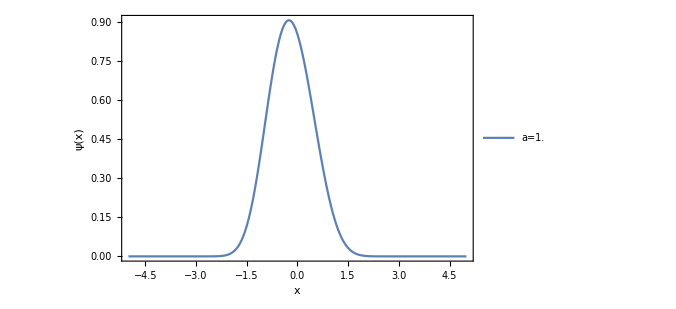

```mathematica
points=Table[Numerov[V,-5,5,a,200],{a,1,1,0.2}];
legendLabels=Table["a="<>ToString[a],{a,1,1,0.2}];

ListPlot[points,PlotRange->All,Joined->True,FrameStyle->Directive[FontWeight->"Plain",Black,13],Frame->True,FrameLabel->{"x","ψ(x)"},PlotLegends->legendLabels,ImageSize->500]
```

```mathematica
points
```

{{{-5.,0.},{-4.95,0.},{-4.9,0.},{-4.85,0.},{-4.8,0.},{-4.75,0.},{-4.7,0.},{-4.65,0.},{-4.6,0.},{-4.55,0.},{-4.5,0.},{-4.45,0.},{-4.4,0.},{-4.35,0.},{-4.3,0.},{-4.25,0.},{-4.2,0.},{-4.15,0.},{-4.1,0.},{-4.05,0.},{-4.,0.},{-3.95,0.},{-3.9,0.},{-3.85,0.},{-3.8,0.},{-3.75,0.},{-3.7,0.},{-3.65,0.},{-3.6,0.},{-3.55,0.},{-3.5,0.},{-3.45,5.7814×10^-10},{-3.4,1.37516×10^-9},{-3.35,3.19286×10^-9},{-3.3,7.23881×10^-9},{-3.25,1.60315×10^-8},{-3.2,3.46943×10^-8},{-3.15,7.33965×10^-8},{-3.1,1.51838×10^-7},{-3.05,3.07276×10^-7},{-3.,6.0852×10^-7},{-2.95,1.17971×10^-6},{-2.9,2.23964×10^-6},{-2.85,4.16528×10^-6},{-2.8,7.59139×10^-6},{-2.75,0.0000135633},{-2.7,0.0000237643},{-2.65,0.0000408467},{-2.6,0.0000688987},{-2.55,0.000114088},{-2.5,0.00018552},{-2.45,0.00029636},{-2.4,0.000465239},{-2.35,0.000717974},{-2.3,0.0010896},{-2.25,0.0016267},{-2.2,0.00238985},{-2.15,0.00345628},{-2.1,0.00492235},{-2.05,0.00690571},{-2.,0.00954694},{-1.95,0.0130103},{-1.9,0.0174833},{-1.85,0.0231751},{-1.8,0.0303126},{-1.75,0.039136},{-1.7,0.0498913},{-1.65,0.0628217},{-1.6,0.0781584},{-1.55,0.0961087},{-1.5,0.116845},{-1.45,0.140495},{-1.4,0.167129},{-1.35,0.196751},{-1.3,0.229294},{-1.25,0.264615},{-1.2,0.302491},{-1.15,0.342622},{-1.1,0.384639},{-1.05,0.428105},{-1.,0.472531},{-0.95,0.517384},{-0.9,0.562104},{-0.85,0.606117},{-0.8,0.648847},{-0.75,0.689736},{-0.7,0.728251},{-0.65,0.763902},{-0.6,0.796246},{-0.55,0.824899},{-0.5,0.84954},{-0.45,0.869916},{-0.4,0.885842},{-0.35,0.8972},{-0.3,0.903941},{-0.25,0.906077},{-0.2,0.90368},{-0.15,0.896876},{-0.1,0.885837},{-0.05,0.87078},{0.,0.851957},{0.05,0.829652},{0.1,0.804173},{0.15,0.775849},{0.2,0.745023},{0.25,0.712051},{0.3,0.677294},{0.35,0.641114},{0.4,0.603874},{0.45,0.565933},{0.5,0.527637},{0.55,0.489327},{0.6,0.451322},{0.65,0.413929},{0.7,0.37743},{0.75,0.342084},{0.8,0.308123},{0.85,0.275748},{0.9,0.24513},{0.95,0.216407},{1.,0.189682},{1.05,0.165023},{1.1,0.142466},{1.15,0.122012},{1.2,0.103632},{1.25,0.0872679},{1.3,0.0728378},{1.35,0.0602375},{1.4,0.0493457},{1.45,0.0400282},{1.5,0.0321423},{1.55,0.0255413},{1.6,0.0200779},{1.65,0.0156085},{1.7,0.0119957},{1.75,0.00911097},{1.8,0.00683645},{1.85,0.00506612},{1.9,0.00370637},{1.95,0.0026761},{2.,0.00190627},{2.05,0.00133919},{2.1,0.000927526},{2.15,0.000633116},{2.2,0.000425755},{2.25,0.000281971},{2.3,0.000183849},{2.35,0.000117972},{2.4,0.0000744733},{2.45,0.0000462354},{2.5,0.0000282192},{2.55,0.0000169261},{2.6,9.97368×10^-6},{2.65,5.77145×10^-6},{2.7,3.27862×10^-6},{2.75,1.82775×10^-6},{2.8,9.99555×10^-7},{2.85,5.36049×10^-7},{2.9,2.81809×10^-7},{2.95,1.45178×10^-7},{3.,7.32626×10^-8},{3.05,3.62031×10^-8},{3.1,1.75119×10^-8},{3.15,8.28869×10^-9},{3.2,3.83748×10^-9},{3.25,1.73722×10^-9},{3.3,7.68691×10^-10},{3.35,0.},{3.4,0.},{3.45,0.},{3.5,0.},{3.55,0.},{3.6,0.},{3.65,0.},{3.7,0.},{3.75,0.},{3.8,0.},{3.85,0.},{3.9,0.},{3.95,0.},{4.,0.},{4.05,0.},{4.1,0.},{4.15,0.},{4.2,0.},{4.25,0.},{4.3,0.},{4.35,0.},{4.4,0.},{4.45,0.},{4.5,0.},{4.55,0.},{4.6,0.},{4.65,0.},{4.7,0.},{4.75,0.},{4.8,0.},{4.85,0.},{4.9,0.},{4.95,0.},{5.,0.}}}

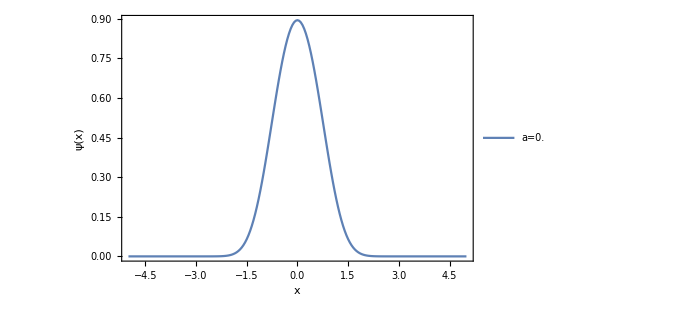

```mathematica
points=Table[Numerov[V,-5,5,a,200],{a,0,0,0.2}];
legendLabels=Table["a="<>ToString[a],{a,0,0,0.2}];

ListPlot[points,PlotRange->All,Joined->True,FrameStyle->Directive[FontWeight->"Plain",Black,13],Frame->True,FrameLabel->{"x","ψ(x)"},PlotLegends->legendLabels,ImageSize->500]
```

```mathematica
points
```

{{{-5.,0.},{-4.95,0.},{-4.9,0.},{-4.85,0.},{-4.8,0.},{-4.75,0.},{-4.7,0.},{-4.65,0.},{-4.6,0.},{-4.55,0.},{-4.5,0.},{-4.45,0.},{-4.4,0.},{-4.35,0.},{-4.3,0.},{-4.25,0.},{-4.2,0.},{-4.15,0.},{-4.1,0.},{-4.05,0.},{-4.,0.},{-3.95,0.},{-3.9,0.},{-3.85,0.},{-3.8,0.},{-3.75,0.},{-3.7,0.},{-3.65,0.},{-3.6,0.},{-3.55,0.},{-3.5,0.},{-3.45,0.},{-3.4,4.74175×10^-10},{-3.35,1.11158×10^-9},{-3.3,2.54481×10^-9},{-3.25,5.6917×10^-9},{-3.2,1.24411×10^-8},{-3.15,2.65867×10^-8},{-3.1,5.55668×10^-8},{-3.05,1.13623×10^-7},{-3.,2.27393×10^-7},{-2.95,4.45554×10^-7},{-2.9,8.55054×10^-7},{-2.85,1.60772×10^-6},{-2.8,2.96283×10^-6},{-2.75,5.35348×10^-6},{-2.7,9.48754×10^-6},{-2.65,0.0000164973},{-2.6,0.0000281558},{-2.55,0.0000471814},{-2.5,0.0000776563},{-2.45,0.000125585},{-2.4,0.000199621},{-2.35,0.000311987},{-2.3,0.000479598},{-2.25,0.00072541},{-2.2,0.00107995},{-2.15,0.00158305},{-2.1,0.00228561},{-2.05,0.00325145},{-2.,0.00455902},{-1.95,0.0063028},{-1.9,0.00859434},{-1.85,0.0115627},{-1.8,0.0153538},{-1.75,0.0201296},{-1.7,0.0260651},{-1.65,0.0333456},{-1.6,0.0421613},{-1.55,0.0527024},{-1.5,0.0651524},{-1.45,0.079681},{-1.4,0.096437},{-1.35,0.115541},{-1.3,0.137078},{-1.25,0.161092},{-1.2,0.187581},{-1.15,0.216492},{-1.1,0.247721},{-1.05,0.281111},{-1.,0.316453},{-0.95,0.35349},{-0.9,0.391921},{-0.85,0.431408},{-0.8,0.471579},{-0.75,0.512039},{-0.7,0.552378},{-0.65,0.592175},{-0.6,0.631009},{-0.55,0.668467},{-0.5,0.704147},{-0.45,0.737669},{-0.4,0.768675},{-0.35,0.796837},{-0.3,0.821859},{-0.25,0.843481},{-0.2,0.86148},{-0.15,0.875672},{-0.1,0.885913},{-0.05,0.892098},{0.,0.894167},{0.05,0.892098},{0.1,0.885913},{0.15,0.875672},{0.2,0.86148},{0.25,0.843481},{0.3,0.821859},{0.35,0.796837},{0.4,0.768675},{0.45,0.737669},{0.5,0.704147},{0.55,0.668467},{0.6,0.631009},{0.65,0.592175},{0.7,0.552378},{0.75,0.512039},{0.8,0.471579},{0.85,0.431408},{0.9,0.391921},{0.95,0.35349},{1.,0.316453},{1.05,0.281111},{1.1,0.247721},{1.15,0.216492},{1.2,0.187581},{1.25,0.161092},{1.3,0.137078},{1.35,0.115541},{1.4,0.096437},{1.45,0.079681},{1.5,0.0651524},{1.55,0.0527024},{1.6,0.0421613},{1.65,0.0333456},{1.7,0.0260651},{1.75,0.0201296},{1.8,0.0153538},{1.85,0.0115627},{1.9,0.00859434},{1.95,0.0063028},{2.,0.00455902},{2.05,0.00325145},{2.1,0.00228561},{2.15,0.00158305},{2.2,0.00107995},{2.25,0.00072541},{2.3,0.000479598},{2.35,0.000311987},{2.4,0.000199621},{2.45,0.000125585},{2.5,0.0000776563},{2.55,0.0000471814},{2.6,0.0000281558},{2.65,0.0000164973},{2.7,9.48754×10^-6},{2.75,5.35348×10^-6},{2.8,2.96283×10^-6},{2.85,1.60772×10^-6},{2.9,8.55054×10^-7},{2.95,4.45554×10^-7},{3.,2.27393×10^-7},{3.05,1.13623×10^-7},{3.1,5.55668×10^-8},{3.15,2.65867×10^-8},{3.2,1.24411×10^-8},{3.25,5.6917×10^-9},{3.3,2.54481×10^-9},{3.35,1.11158×10^-9},{3.4,4.74176×10^-10},{3.45,0.},{3.5,0.},{3.55,0.},{3.6,0.},{3.65,0.},{3.7,0.},{3.75,0.},{3.8,0.},{3.85,0.},{3.9,0.},{3.95,0.},{4.,0.},{4.05,0.},{4.1,0.},{4.15,0.},{4.2,0.},{4.25,0.},{4.3,0.},{4.35,0.},{4.4,0.},{4.45,0.},{4.5,0.},{4.55,0.},{4.6,0.},{4.65,0.},{4.7,0.},{4.75,0.},{4.8,0.},{4.85,0.},{4.9,0.},{4.95,0.},{5.,0.}}}

## Rutina Numerov

Esta rutina funciona bien para nuestro potencial en particular porque es una función de dos argumentos.

```mathematica
Numerov[V_,x0_,xf_,a_,n_]:=Module[{d,x,Ν,A,B,InvB,NumerovK,Voperator,eigE,eigStates,H},
(*Cantidad de puntos (distinto a intervalos)*)
Ν=n+1;

(*Espaciado*)
d=N[(xf-x0)/n];

(*Valores de x en una malla en [x0,xf] con Ν puntos*)
x=Table[x0+d*h,{h,0,n}];

(*Matriz A*)
A=N[(Im1[Ν]-2Id[Ν]+I1[Ν])/d^2];

(*Calcular matriz B y su inversa*)
B=N[(Im1[Ν]+10.Id[Ν]+I1[Ν])/12.];InvB=Inverse[B];

(*Definir al operador cinético de Numerov*)
NumerovK=0.5InvB.A;

(*Definir al operador de potencial*)
Voperator=SparseArray[DiagonalMatrix[V[x,a]]];

(*Definir al operador Hamiltoniano*)
H=-NumerovK+Voperator;

(*Calcular el espectro*)
{eigE,eigStates}=Reverse/@Chop[Eigensystem[H]];
eigStates=eigStates/Sqrt[d];

(*Print[Chop[(H-eigE[[1]]IdentityMatrix[Ν]).eigStates[[1]]]];*)
(*eigE[[30]]*)

(*ojo le meti un abs*)
(*Flatten[Table[Transpose[Append[{x},eigStates[[i]]]],{i,30,30}],1]*)

{eigE,eigStates}

]
```

#### Ojo arriba le metí un abs

```mathematica
points=Table[{a,Numerov[V,-5,5,a,200]},{a,-1,1,0.1}];
legendLabels=Table["a="<>ToString[a],{a,-1,1,0.2}];
```

```mathematica
points
```

{{-1.,0.818002},{-0.8,0.856685},{-0.6,0.886994},{-0.4,0.908766},{-0.2,0.921879},{0.,0.926258},{0.2,0.921879},{0.4,0.908766},{0.6,0.886994},{0.8,0.856685},{1.,0.818002}}

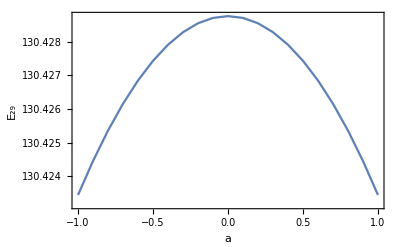

```mathematica
ListPlot[points,PlotRange->Full,Joined->True,Frame->True,FrameLabel->{"a","E_29"},FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,13],LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->13]]
```

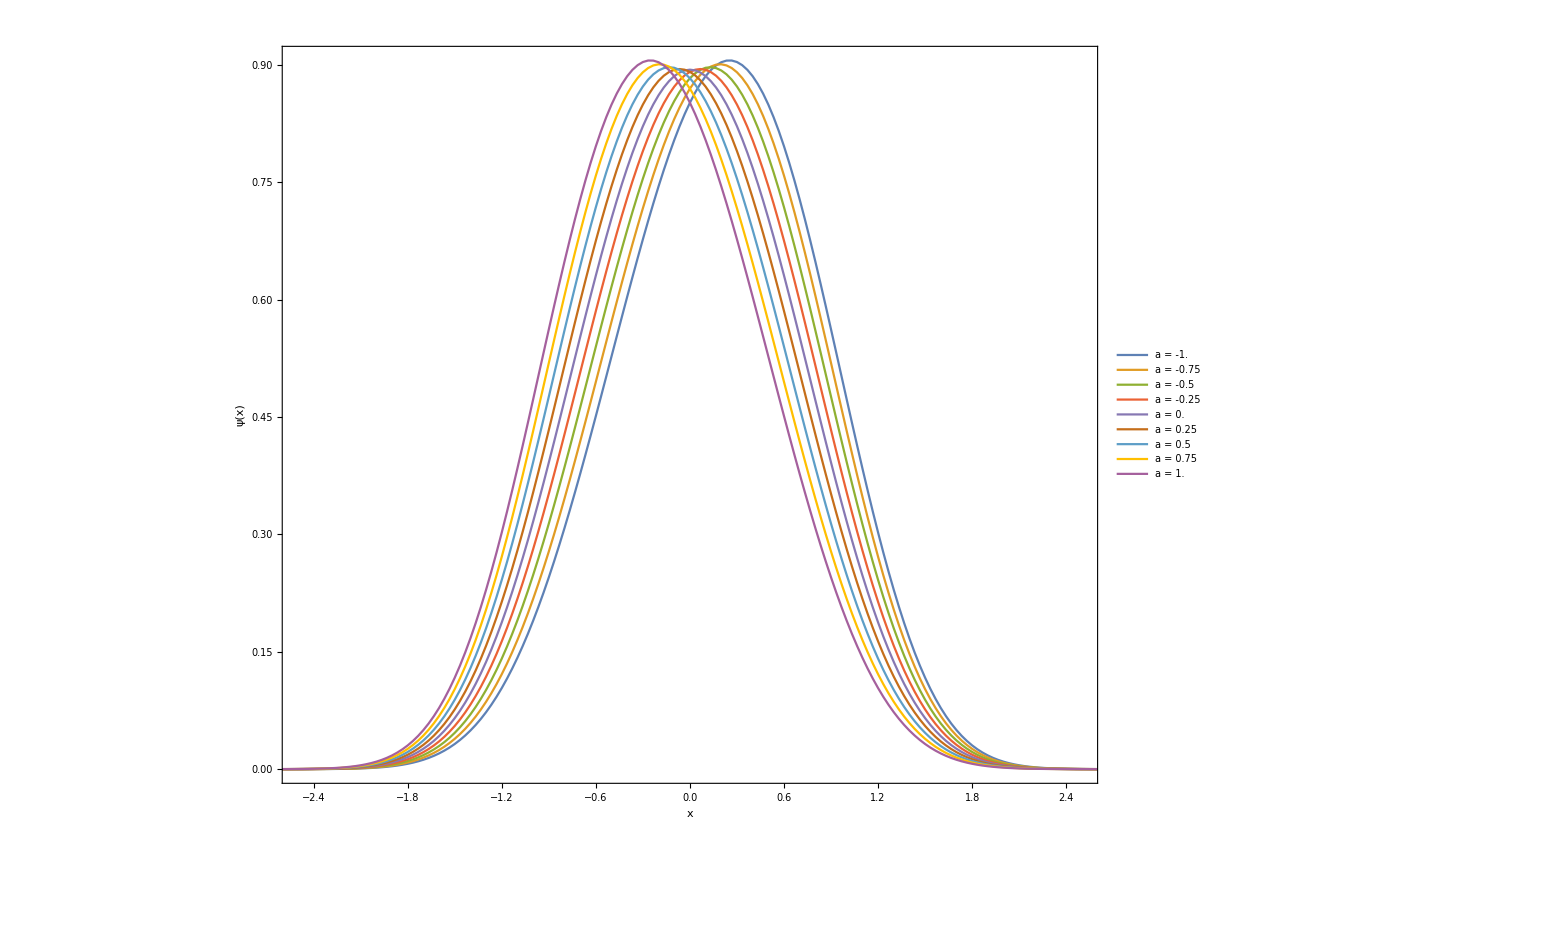

```mathematica
points=Table[Numerov[V,-5,5,a,300],{a,-1,1,0.25}];
legendLabels=Table["a = "<>ToString[a],{a,-1,1,0.25}];

ListPlot[points,PlotRange->{{-2.5,2.5},Automatic},Joined->True,FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,30],Frame->True,FrameLabel->{"x","ψ(x)"},PlotLegends->legendLabels,LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->30],ImageSize->1500]
```

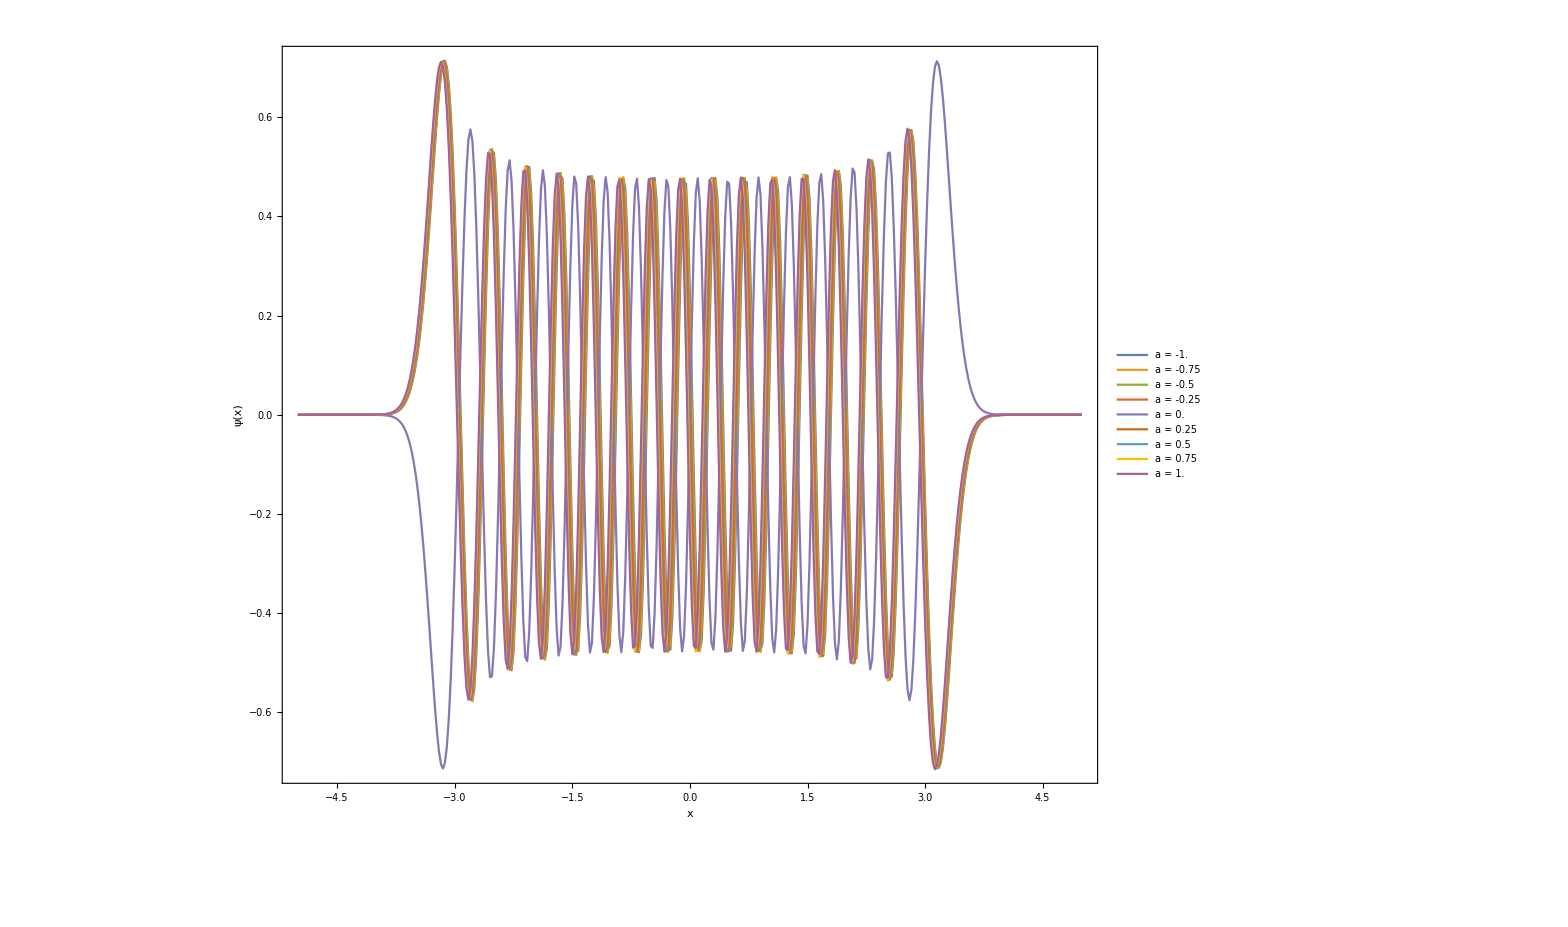

```mathematica
points=Table[Numerov[V,-5,5,a,400],{a,-1,1,0.25}];
legendLabels=Table["a = "<>ToString[a],{a,-1,1,0.25}];

ListPlot[points,PlotRange->Full,Joined->True,FrameStyle->Directive[FontFamily->"Sans Serif",FontWeight->"Plain",Black,30],Frame->True,FrameLabel->{"x","ψ(x)"},PlotLegends->legendLabels,LabelStyle->Directive[FontFamily->"Sans Serif",Black, FontSize->30],ImageSize->1500]
```

```mathematica
¨
```

## Presentación de resultados

```mathematica
{eigE,eigStates}=Numerov[V,-5,5,-1,400];
```

```mathematica
pointsS=eigE[[1]]+eigStates[[1]]
```

```mathematica
pointsV=Transpose[{vx,V[vx,-1]}];
```

```mathematica
vx=points[[1,;;,1]];
```

```mathematica
pointsS=Table[Transpose[{vx,eigE[[i]]+eigStates[[i]]}],{i,30}];
```

```mathematica
lines=Table[Line[{{-4,eigE[[i]]},{4,eigE[[i]]}}],{i,30}];
```

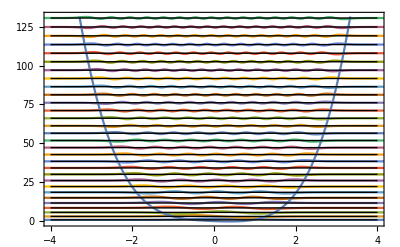

```mathematica
ListPlot[Append[pointsS,pointsV],PlotRange->{{-4,4},{-0.5,eigE[[30]]+1}},Epilog->{ lines,Inset[ListPlot[Append[{pointsS[[1]]},pointsV],PlotRange->{{-2,2},{-0.5,eigE[[1]]+1}},Joined->True,Frame->True,ImageSize->280],{3.3,12}],Inset[ListPlot[Append[{pointsS[[30]]},pointsV],PlotRange->{{-4,4},{eigE[[30]]-1,eigE[[30]]+1}},Joined->True,Frame->True,ImageSize->288],{3.28,35}]},Joined->True,Frame->True,ImageSize->Full]
```